## Crypto Protocol message m = 2

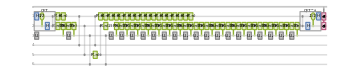

<|00→2.31201×10^-12,01→0.,10→1.,11→0.|>

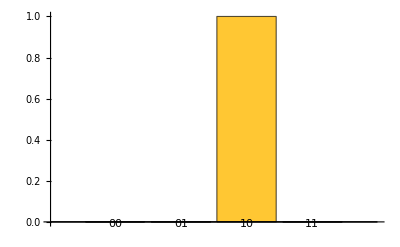

```mathematica
Needs["Wolfram`QuantumFramework`"]
p=0.998489;
q=0.119545;

A=QuantumOperator[{{Sqrt[p],Sqrt[1-p]},{Sqrt[1-p],-Sqrt[p]}}];
B=QuantumOperator[{{Sqrt[q],Sqrt[1-q]},{Sqrt[1-q],-Sqrt[q]}}];

qc = QuantumCircuitOperator[{{"Fourier", 2}, B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}],"P"[-Pi]->5 , QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], {"InverseFourier", 2},{1,2}}];
qc["Diagram",FontSize->4]
FullSimplify/@qc[]["Probabilities"]
qc[]["ProbabilitiesPlot"]
```

## Message m = 1

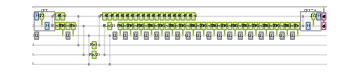

<|00→0.,01→1.,10→0.,11→2.31201×10^-12|>

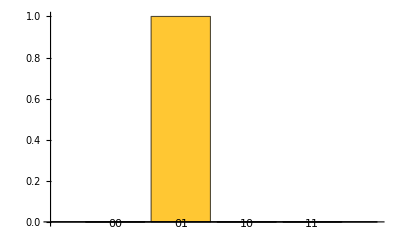

```mathematica
p=0.998489;
q=0.119545;

A=QuantumOperator[{{Sqrt[p],Sqrt[1-p]},{Sqrt[1-p],-Sqrt[p]}}];
B=QuantumOperator[{{Sqrt[q],Sqrt[1-q]},{Sqrt[1-q],-Sqrt[q]}}];

qc = QuantumCircuitOperator[{{"Fourier", 2}, B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}],"P"[Pi]-> 4,"P"[Pi/2]->5 , QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], {"InverseFourier", 2},{1,2}}];
qc["Diagram",FontSize->4]
FullSimplify/@qc[]["Probabilities"]
qc[]["ProbabilitiesPlot"]
```

## Message m = 3

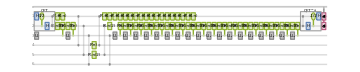

<|00→0.,01→2.31201×10^-12,10→0.,11→1.|>

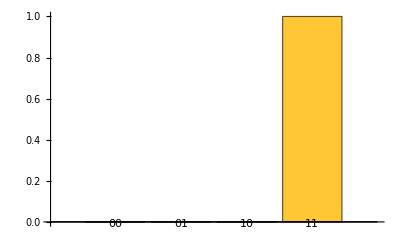

```mathematica
p=0.998489;
q=0.119545;

A=QuantumOperator[{{Sqrt[p],Sqrt[1-p]},{Sqrt[1-p],-Sqrt[p]}}];
B=QuantumOperator[{{Sqrt[q],Sqrt[1-q]},{Sqrt[1-q],-Sqrt[q]}}];

qc = QuantumCircuitOperator[{{"Fourier", 2}, B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}],"P"[Pi]-> 4,"P"[-Pi/2]->5 , QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], {"InverseFourier", 2},{1,2}}];
qc["Diagram",FontSize->4]
FullSimplify/@qc[]["Probabilities"]
qc[]["ProbabilitiesPlot"]
```

## message m = 0

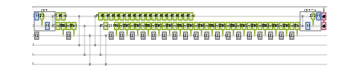

<|00→1.,01→0.,10→2.31201×10^-12,11→0.|>

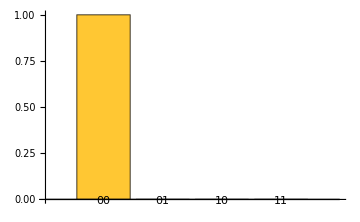

```mathematica
p=0.998489;
q=0.119545;

A=QuantumOperator[{{Sqrt[p],Sqrt[1-p]},{Sqrt[1-p],-Sqrt[p]}}];
B=QuantumOperator[{{Sqrt[q],Sqrt[1-q]},{Sqrt[1-q],-Sqrt[q]}}];

qc = QuantumCircuitOperator[{{"Fourier", 2}, B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}], QuantumOperator["SWAP",{1,4}], QuantumOperator["SWAP", {2,5}], QuantumOperator["SWAP",{3,6}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],B-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}],A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], A-> 3, "P"[-Pi]-> 1,"P"[-Pi/2]-> 2,QuantumOperator["CP"[Pi],{3,2}], {"InverseFourier", 2},{1,2}}];
qc["Diagram",FontSize->4]
FullSimplify/@qc[]["Probabilities"]
qc[]["ProbabilitiesPlot"]
```